## Letting Mathematica do the work in Problem Set 7, Problem 1

The quadratic function we are minimizing.

```mathematica
f[a_, b_]:=(0-(15*a+b))^2+(2.5-(25*a+b))^2+(4.5-(35*a+b))^2
```

A visualization of the function. On the horizontal axis is b. On the vertical axis is a. The colors tell you how high the quadratic function is. Dark colors are low. Orangy colors are high.

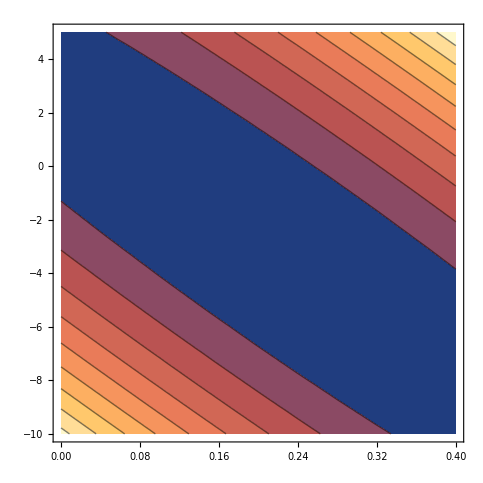

```mathematica
ContourPlot[f[a, b], {a, 0.0, 0.4 }, {b, -10, 5}]
```

It is a little hard to see where the minimum is just by eye-balling it, but Mathematica can find it in one line.

```mathematica
Minimize[f[a, b],{a, b}]
```

{0.0416667,{a→0.225,b→-3.29167}}

Plot the three data points.

```mathematica
plot1=ListPlot[{{15, 59}, {25, 61.5}, {35, 63.5}}, PlotRange->{{0,45},{55, 66}}];
```

The best fit has a=0.225, and b=-3.29, but now I will add the 59 back in, and then b=55.71.

```mathematica
plot2=Plot[0.225*t + 55.71, {t, 0, 60}, PlotRange->{{0, 45},{55, 66}}];
```

Now that we have plotted the data and the best fit,  we display them on top of each other:

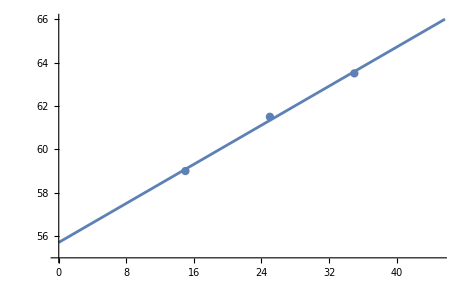

```mathematica
Show[plot1, plot2]
```